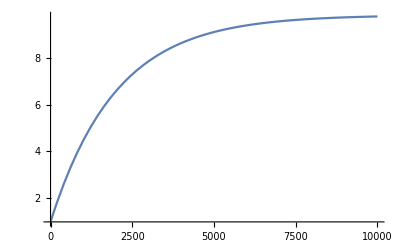

```mathematica
rho=1000;
g=9.81;
a=100;
qin=5;
r=20;
tend=10000;
s=NDSolve[{D[p[t],t]==rho*g/a/10^5*qin-p[t]/a/r,p[0]==1},p,{t,0,tend}];
Plot[Evaluate[p[t]/.s],{t,0,tend},PlotRange->All]
```

```mathematica
SetDirectory["C:\\Users\\Tim\\Documents\\GitHub\\I000864_modsim\\exercises\\SlidesInleidingsLessen\\P1_Massabalansen"];
Export["pwatertoren.dat",Transpose[{Table[i,{i,0,tend,10}],Flatten[Map[Evaluate[p[#]/.s]&,Table[i,{i,0,tend,10}]]]}]];
```

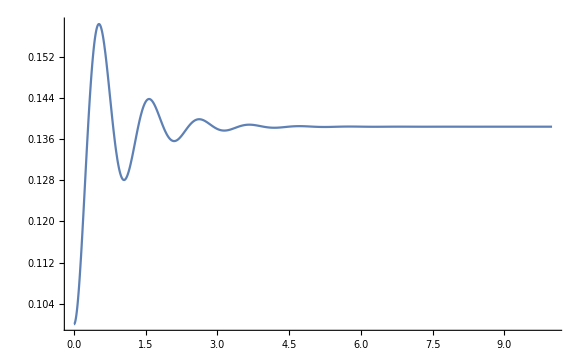

```mathematica
m=80;
k=3000;
l=0.4;
b=200;
fe=0;
g=9.81;
tend=10;

s2=NDSolve[{m*D[x[t],t,t]==fe-m*g+k*(l-x[t])-b*D[x[t],t],x[0]==0.1,x'[0]==0},x,{t,0,tend}];
Plot[Evaluate[x[t]/.s2],{t,0,tend},PlotRange->All]
```

```mathematica
Export["xstoel.dat",Transpose[{Table[i,{i,0,tend,0.02}],Flatten[Map[Evaluate[x[#]/.s2]&,Table[i,{i,0,tend,0.02}]]]}]];
```

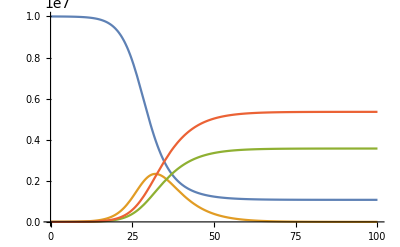

```mathematica
Clear[s,r]
n=10000000;
I0=1000;
beta=10^(-6);
alpha=0.05;
m=0.6;
rp=0.2;

tend=100;


s3=NDSolve[{D[s[t],t]==-alpha*beta*i[t]*s[t],D[i[t],t]==alpha*beta*i[t]*s[t]-rp*i[t],D[d[t],t]==m*rp*i[t],D[r[t],t]==(1-m)*rp*i[t],s[0]==n-I0,i[0]==I0,r[0]==0,d[0]==0},{s,i,r,d},{t,0,tend}];

Plot[Evaluate[{s[t],i[t],r[t],d[t]}/.s3],{t,0,tend},PlotRange->All]
```

```mathematica
Export["ssird.dat",Transpose[{Table[i,{i,0,tend,0.5}],Flatten[Map[Evaluate[s[#]/.s3]&,Table[i,{i,0,tend,0.5}]]]}]];
Export["isird.dat",Transpose[{Table[i,{i,0,tend,0.5}],Flatten[Map[Evaluate[i[#]/.s3]&,Table[i,{i,0,tend,0.5}]]]}]];
Export["dsird.dat",Transpose[{Table[i,{i,0,tend,0.5}],Flatten[Map[Evaluate[d[#]/.s3]&,Table[i,{i,0,tend,0.5}]]]}]];
Export["rsird.dat",Transpose[{Table[i,{i,0,tend,0.5}],Flatten[Map[Evaluate[r[#]/.s3]&,Table[i,{i,0,tend,0.5}]]]}]];
```